#### Problem 1

Since  (2tCos[t])^2+(2tSin[t])^2=4 t^2 increases with respect to t, to plot the part within the Disk[{0,0},3], we only need to let 4 t^2≤ 3^2

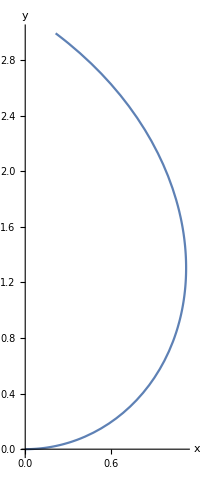

```mathematica
ParametricPlot[{2t Cos[t],2t Sin[t]},{t,0,3/2},AxesLabel->{"x", "y"}]
```

We can also draw out the disk.

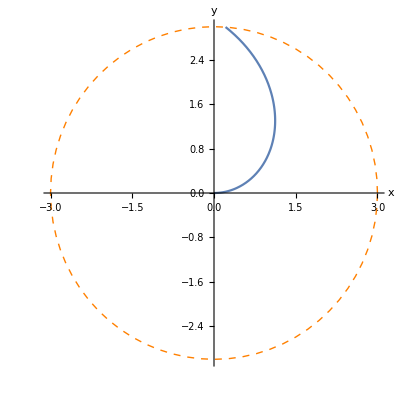

```mathematica
ParametricPlot[{2t Cos[t],2t Sin[t]},{t,0,3/2},AxesLabel->{"x", "y"},Epilog->{Orange,Dashed,Circle[{0,0},3]},PlotRange->{{-3,3},{-3,3}}]
```

#### Problem 2

```mathematica
Show[
ParametricPlot3D[{u+v,3u-v,-2u+v},{u,-2,2},{v,-2,2},ViewPoint->{-4, 2, 3}],
Graphics3D[{Red,Thick,Line[{{0,-8,-6},{0,8,6}}]}]]
```

-Graphics3D-